#### Dimensionful 2D dynamical model for feedback

```mathematica
A1= {{ 0,λ},{-κ2, κ1}}
B1 = {{σx,0},{0,κ2*σy }}
Eigenvalues[A1]
Eigenvectors[A1]
s=Array[X,{2,2}]
s/. Expand[Solve[A1.s+s.Transpose[A1]==B1.Transpose[B1], Flatten[s]]]
```

{{0,λ},{-κ2,κ1}}

{{σx,0},{0,κ2 σy}}

{1/2 (κ1-√(κ1^2-4 κ2 λ)),1/2 (κ1+√(κ1^2-4 κ2 λ))}

{{-(-κ1-√(κ1^2-4 κ2 λ))/(2 κ2),1},{-(-κ1+√(κ1^2-4 κ2 λ))/(2 κ2),1}}

{{X[1,1],X[1,2]},{X[2,1],X[2,2]}}

{{{σx^2/(2 κ1)+(κ1 σx^2)/(2 κ2 λ)+(κ2 λ σy^2)/(2 κ1),σx^2/(2 λ)},{σx^2/(2 λ),(κ2 σx^2)/(2 κ1 λ)+(κ2^2 σy^2)/(2 κ1)}}}

#### Dimensionless feedback

```mathematica
A3= {{ 0,λt},{-κt, κt}}
B3 = {{1,0},{0,κt }}
Eigenvalues[A3]
eigens = FullSimplify[Eigenvectors[A3]]
s3=Array[Y,{2,2}]
s3/. Expand[FullSimplify[Solve[A3.s3+s3.Transpose[A3]==B3.Transpose[B3], Flatten[s3]]]]
```

{{0,λt},{-κt,κt}}

{{1,0},{0,κt}}

{1/2 (κt-√κt √(κt-4 λt)),1/2 (κt+√κt √(κt-4 λt))}

{{1/2 (1+(√(κt-4 λt))/(√κt)),1},{1/2-(√(κt-4 λt))/(2 √κt),1}}

{{Y[1,1],Y[1,2]},{Y[2,1],Y[2,2]}}

{{{1/(2 κt)+1/(2 λt)+λt/2,1/(2 λt)},{1/(2 λt),κt/2+1/(2 λt)}}}

```mathematica
FullSimplify[(MatrixExp[-A3*t].{x0, y0})]
```

{ⅇ^(-(t κt)/2) (x0 Cosh[1/2 t √κt √(κt-4 λt)]+((x0 κt-2 y0 λt) Sinh[1/2 t √κt √(κt-4 λt)])/(√κt √(κt-4 λt))),ⅇ^(-(t κt)/2) (y0 Cosh[1/2 t √κt √(κt-4 λt)]+((2 x0-y0) √κt Sinh[1/2 t √κt √(κt-4 λt)])/(√(κt-4 λt)))}

```mathematica
Manipulate[Show[{ParametricPlot[%8, {t, 0, 100}, PlotRange->10], Plot[{(1/2 (1+(√(κt-4 λt))/(√κt)))^-1 x,(1/2 (1-(√(κt-4 λt))/(√κt)))^-1 x}, {x, 0, 10}, PlotStyle->Dashed]}], {λt, 0.05, 0.2}, {κt, 5, 10}, {x0, 1, 8}, {y0, 1, 8}]
```

#### Dimensionless, unamplified noise model

```mathematica
A= {{ 0,λt},{-κt, 1}}
```

{{0,λt},{-κt,1}}

```mathematica
X0={x0, y0}
```

{x0,y0}

```mathematica
FullSimplify[Eigenvectors[A]]
```

{{(1+√(1-4 κt λt))/(2 κt),1},{-(-1+√(1-4 κt λt))/(2 κt),1}}

```mathematica
Eigenvalues[A]
```

{1/2 (1-√(1-4 κt λt)),1/2 (1+√(1-4 κt λt))}

```mathematica
MatrixExp[-A*t].X0
```

{y0 ((ⅇ^(1/2 t (-1-√(1-4 κt λt))) λt)/(√(1-4 κt λt))-(ⅇ^(1/2 t (-1+√(1-4 κt λt))) λt)/(√(1-4 κt λt)))+x0 (-(ⅇ^(1/2 t (-1-√(1-4 κt λt))) (1-√(1-4 κt λt)))/(2 √(1-4 κt λt))+(ⅇ^(1/2 t (-1+√(1-4 κt λt))) (1+√(1-4 κt λt)))/(2 √(1-4 κt λt))),x0 (-(ⅇ^(1/2 t (-1-√(1-4 κt λt))) κt)/(√(1-4 κt λt))+(ⅇ^(1/2 t (-1+√(1-4 κt λt))) κt)/(√(1-4 κt λt)))+y0 (-(ⅇ^(1/2 t (-1-√(1-4 κt λt))) (-1-√(1-4 κt λt)))/(2 √(1-4 κt λt))+(ⅇ^(1/2 t (-1+√(1-4 κt λt))) (-1+√(1-4 κt λt)))/(2 √(1-4 κt λt)))}

```mathematica
X[t_, x0_, y0_, λt_] = FullSimplify[%]
```

{ⅇ^(-t/2) (x0 Cosh[1/2 t √(1-4 κt λt)]+((x0-2 y0 λt) Sinh[1/2 t √(1-4 κt λt)])/(√(1-4 κt λt))),ⅇ^(-t/2) (y0 Cosh[1/2 t √(1-4 κt λt)]+((-y0+2 x0 κt) Sinh[1/2 t √(1-4 κt λt)])/(√(1-4 κt λt)))}

```mathematica
Manipulate[Show[{ParametricPlot[X[t, x0, y0, λt], {t, 0, 100}, PlotRange->3], Plot[{((1+√(1-4 κt λt))/(2 κt))^-1 x,((1-√(1-4 κt λt))/(2 κt))^-1 x, 1}, {x, 0, 3}, PlotStyle->Dashed]}], {λt, 0.001, 0.24}, {κt, 0.1, 10},{x0, 1.01, 2}, {y0, 1.01, 2}]
```

#### Solve for the time y(t*)=1 and evaluate x(t*).

```mathematica
λs = {0.01, 0.02, 0.05, 0.1};
x0h = 1.5;
Δ=0.01;
varAndMeanFunc[λt0_, x0h_,Δ_]:=Module[{c, cf,y0h, x0Range, y0Range, params, tSolver, tvals, results, res,xpoints, grid, f},
c=2/(1+Sqrt[1-4λt0]);
cf = 2/(1+Sqrt[1-4λ]);
y0h =x0h*c;
x0Range = Table[p, {p, x0h-Δ, x0h+Δ, 0.005}];
y0Range = Table[p, {p,y0h-Δ, y0h+Δ, 0.005}];
params = Flatten[Table[{x0->x, y0->y, λt->λt0}, {x, x0Range}, {y, y0Range}], 1];
tSolver [params_]:=FindRoot[(ⅇ^(-t/2) (y0 Cosh[1/2 t √(1-4 λt)]+((2 x0-y0) Sinh[1/2 t √(1-4 λt)])/(√(1-4 λt)))==1)/.params, {t,(1/λt)/.params}, AccuracyGoal->16, PrecisionGoal->16][[1]];
tvals = MapThread[tSolver, {params}];
results = Transpose[{params, tvals}];
res = Table[AppendTo[r[[1]], r[[2]]], {r, results}];
xpoints =Table[ⅇ^(-t/2) (x0 Cosh[1/2 t √(1-4 λt)]+((x0-2 y0 λt) Sinh[1/2 t √(1-4 λt)])/(√(1-4 λt)))/.p, {p, res}];
grid = Flatten[Table[{x,y}, {x, x0Range}, {y, y0Range}], 1];
f = Interpolation[Transpose[{grid, xpoints}]];
Return[{f, x0h, y0h, c}];]
```

```mathematica
results=Table[varAndMeanFunc[l, x0h, Δ], {l,λs}]
```

{{InterpolatingFunction[…],1.5,1.51531,1.01021},{InterpolatingFunction[…],1.5,1.53126,1.02084},{InterpolatingFunction[…],1.5,1.58359,1.05573},{InterpolatingFunction[…],1.5,1.69052,1.12702}}

```mathematica
{f, x0h, y0h, c} = results[[4]]
```

{InterpolatingFunction[…],1.5,1.69052,1.12702}

```mathematica
Plot3D[f[x,y], {x,x0h-Δ, x0h+Δ}, {y, y0h-Δ, y0h+Δ}, AxesLabel->{"x", "y"}]
```

-Graphics3D-

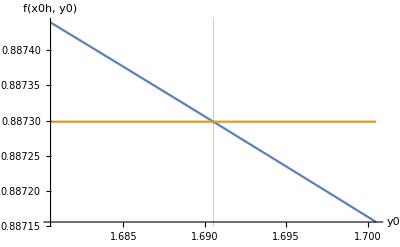

```mathematica
Show[{Plot[{f[x0h, y], 1/c},  {y, y0h-Δ, y0h+Δ}, AxesLabel->{"y0", "f(x0h, y0)"}, GridLines-> {{{y0h,Red}},None}]}]
```

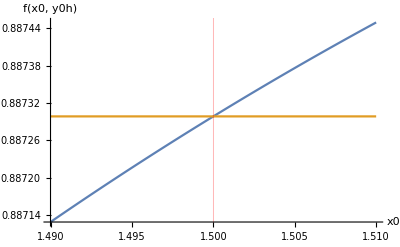

```mathematica
Plot[{f[x, y0h],1/c},  {x, x0h-Δ, x0h+Δ}, AxesLabel->{"x0", "f(x0, y0h)"}, GridLines-> {{{x0h,Red}},None}]
```

```mathematica
dFunction[f_,x0h_, y0h_, sigmaX_, sigmaY_]:=Module[{hess, fyy, fxx, fy, fx, fval},
hess = ({{D[f[x, y], {x,2}],D[f[x, y], x,y]},{D[f[x, y], x,y],D[f[x, y], {y,2}]}})/.{x->x0h, y->y0h};
fyy = hess[[2,2]];
fxx = hess[[1,1]];
fy = D[f[x, y], {y}]/.{x->x0h, y->y0h};
fx = D[f[x, y], {x}]/.{x->x0h, y->y0h};
fval = f[x, y]/.{x->x0h, y->y0h};
Return[{ sigmaY^2 fy^2,fval+sigmaY^2 fyy/2, sigmaX^2 fx^2, fval+sigmaX^2 fxx/2 }];]
```

#### width and mean with sy, lambda

```mathematica
MapThread[dFunction,{Transpose[results][[1]], Transpose[results][[2]], Transpose[results][[3]], Table[sx, 4],Table[sy, 4]}]
```

{{1.2326×10^-28 sy^2,0.989898-1.77636×10^-11 sy^2,1.6777×10^-26 sx^2,0.989898-2.44249×10^-11 sx^2},{1.67912×10^-18 sy^2,0.979583-8.4599×10^-10 sy^2,1.74307×10^-18 sx^2,0.979583-4.33675×10^-8 sx^2},{6.13744×10^-8 sy^2,0.947214-0.000164443 sy^2,6.83915×10^-8 sx^2,0.947214-0.00331469 sx^2},{0.000202171 sy^2,0.887298-0.00757969 sy^2,0.000256786 sx^2,0.887298-0.0937514 sx^2}}

```mathematica
m1sx^2/.{x0->1.5, λ->0.1}
```

0.000256791

```mathematica
m1sy^2/.{x0->1.5, λ->0.1}
```

0.000202171

```mathematica
m2sx /. {x0->1.5, λ->0.1}
```

-0.0937356

```mathematica
m2sy /. {x0->1.5, λ->0.1}
```

-0.0075797

```mathematica
Σ[t]=FullSimplify[MatrixExp[-A*t].{{sx0, sxy0},{sxy0, sy0}}.MatrixExp[-Transpose[A]*t]];
VarDiff = FullSimplify[Σ[t][[1,1]]+Σ[t][[2,2]]-Σ[t][[1,2]]];
Σ[t][[1,1]]/.t->(2 Log[1/x0])/(-1+√(1-4 λt));
Manipulate[Plot[%27, {λt, 0.02, 0.24}, PlotRange->{-0.01, 0.1}], {x0, 1.5, 3}, {sx0, 0.1, 1}, {sy0,0.1, 1}, {sxy0, 0, 1}]
```

#### Implicit differentiation for f(x0, y0).

```mathematica
cf = 2/(1+Sqrt[1-4λ])
```

2/(1+√(1-4 λ))

```mathematica
DSolve[{y'[x]==1/λ-x/(λ *y[x])}, y[x], x, Assumptions->{1-4λ>0, λ>0, x>0, y[x]>0}]
```

Solve[-ArcTanh[(-1+(2 λ y[x])/x)/(√(1-4 λ))]/(√(1-4 λ) λ)+Log[1-y[x]/x+(λ y[x]^2)/x^2]/(2 λ)==C[1]-Log[x]/λ,y[x]]

```mathematica
FullSimplify[%, Assumptions->{x>0, y[x]>0, 1-4λ>0, λ>0}]
```

Solve[2 ArcTanh[(x-2 λ y[x])/(x √(1-4 λ))]+√(1-4 λ) (-2 λ C[1]+Log[x^2-x y[x]+λ y[x]^2])==0,y[x]]

```mathematica
FullSimplify[Solve[2 ArcTanh[(x-2 λ y[x])/(x √(1-4 λ))]+√(1-4 λ) (-2 λ C[1]+Log[x^2-x y[x]+λ y[x]^2])==0, C[1]]]
```

{{C[1]→((2 ArcTanh[(x-2 λ y[x])/(x √(1-4 λ))])/(√(1-4 λ))+Log[x^2-x y[x]+λ y[x]^2])/(2 λ)}}

#### First, consider y0 = yh0 + ϵ

```mathematica
gy[δ]=FullSimplify[(2 ArcTanh[(x-2 λ y[x])/(x √(1-4 λ))])/(√(1-4 λ))+Log[x^2-x y[x]+λ y[x]^2]/.{y[x]->1, x-> 1/cf + δ},  Assumptions->{1-4λ>0,λ>0}]
```

(2 ArcTanh[(1+2 δ+√(1-4 λ)-4 λ)/((1+2 δ+√(1-4 λ)) √(1-4 λ))])/(√(1-4 λ))+Log[δ (δ+√(1-4 λ))]

#### Let δ be a power series -m1*ϵ0+m2*ϵ0^2

```mathematica
gys=FullSimplify[Series[TrigToExp[gy[δ]/.δ->-m1*ϵ0+m2*ϵ0^2+m3*ϵ0^3], {ϵ0, 0, 1}, Assumptions->ϵ0∈Reals]]
```

(Log[-m1 ϵ0 √(1-4 λ)]-Log[(2 m1 ϵ0 λ)/(√(1-4 λ) (1+√(1-4 λ)-2 λ))]/(√(1-4 λ)))+((m2+m1^2 (1+√(1-4 λ))-m2 (√(1-4 λ)+4 λ)) ϵ0)/(m1 (-1+4 λ))+O[ϵ0]^2

```mathematica
hy[x0,ϵ0]=FullSimplify[(2 ArcTanh[(x-2 λ y[x])/(x √(1-4 λ))])/(√(1-4 λ))+Log[x^2-x y[x]+λ y[x]^2]/.{y[x]->(cf*x0)+ϵ0, x->x0},Assumptions->{1-4λ>0, x0>0, λ>0}]
```

(2 ArcTanh[1-(2 ϵ0 λ)/(x0 √(1-4 λ))])/(√(1-4 λ))+Log[ϵ0 (-x0 √(1-4 λ)+ϵ0 λ)]

```mathematica
hys =FullSimplify[Series[hy[x0, ϵ0], {ϵ0, 0, 1}, Assumptions->ϵ0∈Reals]]
```

(Log[-x0 ϵ0 √(1-4 λ)]-Log[(ϵ0 λ)/(x0 √(1-4 λ))]/(√(1-4 λ)))-((1+√(1-4 λ)) λ ϵ0)/(x0-4 x0 λ)+O[ϵ0]^2

```mathematica
FullSimplify[Normal@gys==Normal@hys , Assumptions->{0<λ<1/4, λ>0, x0>0, ϵ∈Reals, δ∈Reals}]
```

ϵ0 (m1 x0 (1+√(1-4 λ)-4 λ)-(m2 x0 (-1+√(1-4 λ)) (-1+4 λ))/m1+λ (-1-√(1-4 λ)+4 λ))+x0 (-1+4 λ) (Log[ϵ0]+√(1-4 λ) (Log[-m1 ϵ0]-Log[-x0 ϵ0])-Log[(2 m1 x0 ϵ0)/(1+√(1-4 λ)-2 λ)])==0

#### Solve term-by-term to get first and second derivatives, m1 and m2

Solve by hand for m1

```mathematica
m1sy=((1+Sqrt[1-4λ]-2λ)/(2*x0^(1+Sqrt[1-4λ])))^(1/(1-Sqrt[1-4λ]))
```

2^(-1/(1-√(1-4 λ))) (x0^(-1-√(1-4 λ)) (1+√(1-4 λ)-2 λ))^(1/(1-√(1-4 λ)))

```mathematica
varFuncY[λ_, x0_]:=sy^2((1+Sqrt[1-4λ]-2λ)/(2*x0^(1+Sqrt[1-4λ])))^(1/(1-Sqrt[1-4λ]))
```

```mathematica
(m1 x0 (1+√(1-4 λ)-4 λ)-(m2 x0 (-1+√(1-4 λ)) (-1+4 λ))/m1+λ (-1-√(1-4 λ)+4 λ))/.m1->((1+Sqrt[1-4λ]-2λ)/(2*x0^(1+Sqrt[1-4λ])))^(1/(1-Sqrt[1-4λ]))
```

2^(-1/(1-√(1-4 λ))) x0 (1+√(1-4 λ)-4 λ) (x0^(-1-√(1-4 λ)) (1+√(1-4 λ)-2 λ))^(1/(1-√(1-4 λ)))-2^(1/(1-√(1-4 λ))) m2 x0 (-1+√(1-4 λ)) (x0^(-1-√(1-4 λ)) (1+√(1-4 λ)-2 λ))^(-1/(1-√(1-4 λ))) (-1+4 λ)+λ (-1-√(1-4 λ)+4 λ)

```mathematica
FullSimplify[%]
```

2^(1/(-1+√(1-4 λ))) x0 (1+√(1-4 λ)-4 λ) (x0^(-1-√(1-4 λ)) (1+√(1-4 λ)-2 λ))^(1/(1-√(1-4 λ)))-2^(1/(1-√(1-4 λ))) m2 x0 (-1+√(1-4 λ)) (x0^(-1-√(1-4 λ)) (1+√(1-4 λ)-2 λ))^(1/(-1+√(1-4 λ))) (-1+4 λ)+λ (-1-√(1-4 λ)+4 λ)

```mathematica
Solve[%==0, m2]
```

{{m2→-(2^(-1/(1-√(1-4 λ))) (x0^(-1-√(1-4 λ)) (1+√(1-4 λ)-2 λ))^(-1/(-1+√(1-4 λ))) (-2^(1/(-1+√(1-4 λ))) x0 (1+√(1-4 λ)-4 λ) (x0^(-1-√(1-4 λ)) (1+√(1-4 λ)-2 λ))^(1/(1-√(1-4 λ)))-λ (-1-√(1-4 λ)+4 λ)))/(x0 (-1+√(1-4 λ)) (-1+4 λ))}}

```mathematica
FullSimplify[%, Assumptions->{1/4>λ>0, x0>0}]
```

{{m2→(2^(1/(-1+√(1-4 λ))) (1+√(1-4 λ)-4 λ) (x0^(-1-√(1-4 λ)) (1+√(1-4 λ)-2 λ))^(-2/(-1+√(1-4 λ))) (2^(1/(-1+√(1-4 λ))) x0-(x0^(-1-√(1-4 λ)) (1+√(1-4 λ)-2 λ))^(1/(-1+√(1-4 λ))) λ))/(x0 (-1+√(1-4 λ)) (-1+4 λ))}}

```mathematica
fppFuncY[λ_, x0_]:=2*((2^(1/(-1+√(1-4 λ))) x0^(4/(-1+√(1-4 λ))) (1+√(1-4 λ)-4 λ) (1+√(1-4 λ)-2 λ)^(-2/(-1+√(1-4 λ))) (2^(1/(-1+√(1-4 λ))) x0^2-x0^((1+√(1-4 λ))/(2 λ)) (1+√(1-4 λ)-2 λ)^(1/(-1+√(1-4 λ))) λ))/((-1+√(1-4 λ)) (-1+4 λ)))
```

```mathematica
m2sy = (2^(1/(-1+√(1-4 λ))) (1+√(1-4 λ)-4 λ) (x0^(-1-√(1-4 λ)) (1+√(1-4 λ)-2 λ))^(-2/(-1+√(1-4 λ))) (2^(1/(-1+√(1-4 λ))) x0-(x0^(-1-√(1-4 λ)) (1+√(1-4 λ)-2 λ))^(1/(-1+√(1-4 λ))) λ))/(x0 (-1+√(1-4 λ)) (-1+4 λ))
```

(2^(1/(-1+√(1-4 λ))) (1+√(1-4 λ)-4 λ) (x0^(-1-√(1-4 λ)) (1+√(1-4 λ)-2 λ))^(-2/(-1+√(1-4 λ))) (2^(1/(-1+√(1-4 λ))) x0-(x0^(-1-√(1-4 λ)) (1+√(1-4 λ)-2 λ))^(1/(-1+√(1-4 λ))) λ))/(x0 (-1+√(1-4 λ)) (-1+4 λ))

```mathematica
meanFuncY[λ_, x0_]:=(1+Sqrt[1-4λ])/2+sy^2 fppFuncY[λ, x0]/2
```

```mathematica
sy^2 fpFunc[0.05, 1.5]^2
```

6.13744×10^-8 sy^2

```mathematica
meanFunc[0.05, 1.5]
```

0.947214-0.000164442 sy^2

```mathematica
λrange ={0.001, 0.002, 0.005, 0.01, 0.02, 0.05, 0.1, 0.2};
x0range = {1.01, 1.02, 1.05, 1.1, 1.2, 1.5, 2, 3};
grid = Flatten[Table[{l,x}, {l,λrange},{x, x0range}], 1]
```

{{0.001,1.01},{0.001,1.02},{0.001,1.05},{0.001,1.1},{0.001,1.2},{0.001,1.5},{0.001,2},{0.001,3},{0.002,1.01},{0.002,1.02},{0.002,1.05},{0.002,1.1},{0.002,1.2},{0.002,1.5},{0.002,2},{0.002,3},{0.005,1.01},{0.005,1.02},{0.005,1.05},{0.005,1.1},{0.005,1.2},{0.005,1.5},{0.005,2},{0.005,3},{0.01,1.01},{0.01,1.02},{0.01,1.05},{0.01,1.1},{0.01,1.2},{0.01,1.5},{0.01,2},{0.01,3},{0.02,1.01},{0.02,1.02},{0.02,1.05},{0.02,1.1},{0.02,1.2},{0.02,1.5},{0.02,2},{0.02,3},{0.05,1.01},{0.05,1.02},{0.05,1.05},{0.05,1.1},{0.05,1.2},{0.05,1.5},{0.05,2},{0.05,3},{0.1,1.01},{0.1,1.02},{0.1,1.05},{0.1,1.1},{0.1,1.2},{0.1,1.5},{0.1,2},{0.1,3},{0.2,1.01},{0.2,1.02},{0.2,1.05},{0.2,1.1},{0.2,1.2},{0.2,1.5},{0.2,2},{0.2,3}}

```mathematica
meanValsY = Table[Apply[meanFuncY, a], {a, grid}]
meanValsUncorrectedY= Table[If[Length[m]>1, m[[1]], m],{m, meanValsY}]
varValsY = Table[Apply[varFuncY, a]/sy^2, {a, grid}]
```

{0.998999-0.0000173988 sy^2,0.998999-9.41727×10^-10 sy^2,0.998999-2.49689×10^-22 sy^2,0.998999-1.63771×10^-42 sy^2,0.998999-2.90739×10^-80 sy^2,0.998999,0.998999,0.998999,0.997996+0.000789072 sy^2,0.997996-0.0000186011 sy^2,0.997996-9.81418×10^-12 sy^2,0.997996-8.13588×10^-22 sy^2,0.997996-1.13237×10^-40 sy^2,0.997996-4.96692×10^-89 sy^2,0.997996,0.997996,0.994975+0.472988 sy^2,0.994975+0.00345244 sy^2,0.994975-0.0000221778 sy^2,0.994975-2.1266×10^-9 sy^2,0.994975-6.42619×10^-17 sy^2,0.994975-3.33696×10^-36 sy^2,0.994975-4.58324×10^-61 sy^2,0.994975-4.16775×10^-96 sy^2,0.989898+1.76937 sy^2,0.989898+0.224879 sy^2,0.989898-0.00198158 sy^2,0.989898-0.000029144 sy^2,0.989898-5.31382×10^-9 sy^2,0.989898-1.35614×10^-18 sy^2,0.989898-5.81627×10^-31 sy^2,0.989898-2.1548×10^-48 sy^2,0.979583+2.32842 sy^2,0.979583+0.853475 sy^2,0.979583+0.0280312 sy^2,0.979583-0.00271265 sy^2,0.979583-0.0000480462 sy^2,0.979583-8.64167×10^-10 sy^2,0.979583-6.56453×10^-16 sy^2,0.979583-1.55741×10^-24 sy^2,0.947214+1.50124 sy^2,0.947214+1.01618 sy^2,0.947214+0.303764 sy^2,0.947214+0.0250207 sy^2,0.947214-0.00765277 sy^2,0.947214-0.000164442 sy^2,0.947214-7.11795×10^-7 sy^2,0.947214-3.28442×10^-10 sy^2,0.887298+0.718971 sy^2,0.887298+0.596334 sy^2,0.887298+0.336581 sy^2,0.887298+0.120471 sy^2,0.887298-0.000796885 sy^2,0.887298-0.0075797 sy^2,0.887298-0.000728174 sy^2,0.887298-0.0000205119 sy^2,0.723607+0.184418 sy^2,0.723607+0.169799 sy^2,0.723607+0.131938 sy^2,0.723607+0.0847601 sy^2,0.723607+0.0290813 sy^2,0.723607-0.0163453 sy^2,0.723607-0.0146336 sy^2,0.723607-0.00503337 sy^2}

{0.998999,0.998999,0.998999,0.998999,0.998999,0.998999,0.998999,0.998999,0.997996,0.997996,0.997996,0.997996,0.997996,0.997996,0.997996,0.997996,0.994975,0.994975,0.994975,0.994975,0.994975,0.994975,0.994975,0.994975,0.989898,0.989898,0.989898,0.989898,0.989898,0.989898,0.989898,0.989898,0.979583,0.979583,0.979583,0.979583,0.979583,0.979583,0.979583,0.979583,0.947214,0.947214,0.947214,0.947214,0.947214,0.947214,0.947214,0.947214,0.887298,0.887298,0.887298,0.887298,0.887298,0.887298,0.887298,0.887298,0.723607,0.723607,0.723607,0.723607,0.723607,0.723607,0.723607,0.723607}

{0.0000178962,9.60562×10^-10,2.62173×10^-22,1.80148×10^-42,3.48886×10^-80,6.70792×10^-177,1.37358×10^-301,0.,0.00258961,0.0000191603,1.03048×10^-11,8.94944×10^-22,1.35884×10^-40,7.45034×10^-89,4.49714×10^-151,9.11681×10^-239,0.0511682,0.00727478,0.0000234011,2.3392×10^-9,7.71123×10^-17,5.00531×10^-36,9.16625×10^-61,1.25029×10^-95,0.138053,0.0525736,0.00307017,0.0000321689,6.37592×10^-9,2.034×10^-18,1.16313×10^-30,6.46373×10^-48,0.225879,0.140793,0.0350402,0.00376032,0.0000578311,1.29569×10^-9,1.31234×10^-15,4.67019×10^-24,0.299419,0.250899,0.149141,0.0647234,0.0135823,0.000247739,1.41925×10^-6,9.82267×10^-10,0.320038,0.296152,0.235722,0.163433,0.0823816,0.0142187,0.00147645,0.0000606534,0.302247,0.294551,0.273024,0.241718,0.192476,0.107316,0.0505323,0.0174806}

```mathematica
varArrayY = ArrayReshape[varValsY, {8,8}];
meanArrayUncorrectedY = ArrayReshape[meanValsUncorrectedY, {8, 8}];
meanArrayY = ArrayReshape[meanValsY, {8, 8}];
xticks = Transpose[{{1, 2, 3, 4, 5, 6, 7, 8}, λrange}];
yticks = Transpose[{{1, 2, 3, 4, 5, 6, 7, 8}, x0range}];
```

```mathematica
ArrayPlot[varArrayY, ColorFunction->(Blend[{{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"Var hitting distribution"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, x0}]
Grid[N[Reverse[varArrayY],8]]
```

-Graphics-

0.302247 | 0.294551 | 0.273024 | 0.241718 | 0.192476 | 0.107316 | 0.0505323 | 0.0174806
0.320038 | 0.296152 | 0.235722 | 0.163433 | 0.0823816 | 0.0142187 | 0.00147645 | 0.0000606534
0.299419 | 0.250899 | 0.149141 | 0.0647234 | 0.0135823 | 0.000247739 | 1.41925×10^-6 | 9.82267×10^-10
0.225879 | 0.140793 | 0.0350402 | 0.00376032 | 0.0000578311 | 1.29569×10^-9 | 1.31234×10^-15 | 4.67019×10^-24
0.138053 | 0.0525736 | 0.00307017 | 0.0000321689 | 6.37592×10^-9 | 2.034×10^-18 | 1.16313×10^-30 | 6.46373×10^-48
0.0511682 | 0.00727478 | 0.0000234011 | 2.3392×10^-9 | 7.71123×10^-17 | 5.00531×10^-36 | 9.16625×10^-61 | 1.25029×10^-95
0.00258961 | 0.0000191603 | 1.03048×10^-11 | 8.94944×10^-22 | 1.35884×10^-40 | 7.45034×10^-89 | 4.49714×10^-151 | 9.11681×10^-239
0.0000178962 | 9.60562×10^-10 | 2.62173×10^-22 | 1.80148×10^-42 | 3.48886×10^-80 | 6.70792×10^-177 | 1.37358×10^-301 | 0.

```mathematica
varFuncY[λ, 1.01]
```

2^(-1/(1-√(1-4 λ))) sy^2 (1.01^(-1-√(1-4 λ)) (1+√(1-4 λ)-2 λ))^(1/(1-√(1-4 λ)))

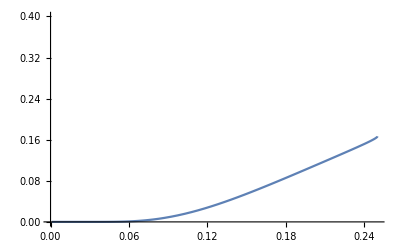

```mathematica
Plot[varFuncY[λ, 1.5]/sy^2, {λ, 0.001, 0.25}, PlotRange->{0, 0.4}]
```

#### With sy, std of hitting distribution

```mathematica
Grid[N[Sqrt[Reverse[varArrayY*0.1^2]],7]]
```

0.054977 | 0.0542725 | 0.0522517 | 0.0491648 | 0.0438721 | 0.0327591 | 0.0224794 | 0.0132214
0.0565719 | 0.0544198 | 0.0485512 | 0.0404268 | 0.0287022 | 0.0119242 | 0.00384246 | 0.000778803
0.0547192 | 0.0500898 | 0.0386188 | 0.0254408 | 0.0116543 | 0.00157397 | 0.000119132 | 3.13411×10^-6
0.0475267 | 0.0375224 | 0.018719 | 0.00613214 | 0.000760467 | 3.59957×10^-6 | 3.62262×10^-9 | 2.16106×10^-13
0.0371555 | 0.0229289 | 0.00554091 | 0.000567176 | 7.98494×10^-6 | 1.42618×10^-10 | 1.07849×10^-16 | 2.54239×10^-25
0.0226204 | 0.00852923 | 0.000483747 | 4.83653×10^-6 | 8.78136×10^-10 | 2.23725×10^-19 | 9.57406×10^-32 | 3.53595×10^-49
0.00508882 | 0.000437724 | 3.21012×10^-7 | 2.99156×10^-12 | 1.16569×10^-21 | 8.63154×10^-46 | 6.70607×10^-77 | 9.5482×10^-121
0.000423039 | 3.09929×10^-6 | 1.61918×10^-12 | 1.34219×10^-22 | 1.86785×10^-41 | 8.19019×10^-90 | 3.70618×10^-152 | 0.

```mathematica
ArrayPlot[meanArrayUncorrectedY, ColorFunction->(Blend[{{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->""],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, x0}]
Grid[N[Reverse[meanArrayUncorrectedY],7]]
```

-Graphics-

0.887298 | 0.887298 | 0.887298 | 0.887298 | 0.887298 | 0.887298 | 0.887298
0.947214 | 0.947214 | 0.947214 | 0.947214 | 0.947214 | 0.947214 | 0.947214
0.979583 | 0.979583 | 0.979583 | 0.979583 | 0.979583 | 0.979583 | 0.979583
0.989898 | 0.989898 | 0.989898 | 0.989898 | 0.989898 | 0.989898 | 0.989898
0.994975 | 0.994975 | 0.994975 | 0.994975 | 0.994975 | 0.994975 | 0.994975
0.997996 | 0.997996 | 0.997996 | 0.997996 | 0.997996 | 0.997996 | 0.997996
0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999

```mathematica
ArrayPlot[meanArrayY/.sy->0.1, ColorFunction->(Blend[{{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->""],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, x0}]
Grid[N[Reverse[meanArrayY/.sy->0.1],7]]
```

-Graphics-

0.894488 | 0.893262 | 0.890664 | 0.888503 | 0.88729 | 0.887223 | 0.887291
0.962226 | 0.957375 | 0.950251 | 0.947464 | 0.947137 | 0.947212 | 0.947214
1.00287 | 0.988118 | 0.979863 | 0.979556 | 0.979583 | 0.979583 | 0.979583
1.00759 | 0.992147 | 0.989878 | 0.989898 | 0.989898 | 0.989898 | 0.989898
0.999705 | 0.995009 | 0.994975 | 0.994975 | 0.994975 | 0.994975 | 0.994975
0.998004 | 0.997996 | 0.997996 | 0.997996 | 0.997996 | 0.997996 | 0.997996
0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999

#### Now do the same for x0->x0h+epsilon

```mathematica
gx[δ]=FullSimplify[(2 ArcTanh[(x-2 λ y[x])/(x √(1-4 λ))])/(√(1-4 λ))+Log[x^2-x y[x]+λ y[x]^2]/.{y[x]->1, x-> 1/cf + δ},  Assumptions->{1-4λ>0,λ>0}]
```

(2 ArcTanh[(1+2 δ+√(1-4 λ)-4 λ)/((1+2 δ+√(1-4 λ)) √(1-4 λ))])/(√(1-4 λ))+Log[δ (δ+√(1-4 λ))]

#### Let δ be a power series m1*ϵ0+m2*ϵ0^2

```mathematica
gxs=FullSimplify[Series[TrigToExp[gx[δ]/.δ->m1*ϵ0+m2*ϵ0^2+m3*ϵ0^3], {ϵ0, 0, 1}, Assumptions->ϵ0∈Reals]]
```

(Log[m1 ϵ0 √(1-4 λ)]-Log[-(2 m1 ϵ0 λ)/(√(1-4 λ) (1+√(1-4 λ)-2 λ))]/(√(1-4 λ)))+((m2+m1^2 (1+√(1-4 λ))-m2 (√(1-4 λ)+4 λ)) ϵ0)/(m1-4 m1 λ)+O[ϵ0]^2

```mathematica
hx[x0,ϵ0]=FullSimplify[(2 ArcTanh[(x-2 λ y[x])/(x √(1-4 λ))])/(√(1-4 λ))+Log[x^2-x y[x]+λ y[x]^2]/.{y[x]->(cf*x0), x->x0+ϵ0},Assumptions->{1-4λ>0, x0>0, λ>0}]
```

(2 ArcTanh[(x0+ϵ0/(√(1-4 λ)))/(x0+ϵ0)])/(√(1-4 λ))+Log[ϵ0 (ϵ0+x0 (2-2/(1+√(1-4 λ))))]

```mathematica
hy[x0, ϵ0]
```

(2 ArcTanh[1-(2 ϵ0 λ)/(x0 √(1-4 λ))])/(√(1-4 λ))+Log[ϵ0 (-x0 √(1-4 λ)+ϵ0 λ)]

```mathematica
hxs =FullSimplify[Series[TrigToExp[hx[x0, ϵ0]], {ϵ0, 0, 1}, Assumptions->{ϵ0∈Reals, 0<λ<1/4, x0>0}]]
```

(Log[x0]+Log[ϵ0]-Log[(ϵ0-ϵ0/(√(1-4 λ)))/(2 x0)]/(√(1-4 λ))+Log[(-1+√(1-4 λ)+4 λ)/(2 λ)])+((1+√(1-4 λ)-2 λ) ϵ0)/(x0-4 x0 λ)+O[ϵ0]^2

```mathematica
FullSimplify[Normal@gxs==Normal@hxs , Assumptions->{0<λ<1/4, λ>0, x0>0, ϵ0∈Reals, δ∈Reals}]
```

ϵ0 (1+√(1-4 λ)-m1 x0 (1+√(1-4 λ)-4 λ)-2 (2+√(1-4 λ)) λ+(m2 x0 (-1+√(1-4 λ)) (-1+4 λ))/m1)+x0 (-1+4 λ) (Log[-ϵ0]-Log[-(2 m1 x0 ϵ0)/(1+√(1-4 λ))]+√(1-4 λ) (-Log[2 x0 ϵ0]+Log[m1 ϵ0 (1+√(1-4 λ))]))==0

#### Solve term-by-term to get first and second derivatives, m1 and m2

Solve by hand for m1

```mathematica
m1sx = ((1+Sqrt[1-4λ])/(2x0))^((1+Sqrt[1-4λ])/(1-Sqrt[1-4λ]))
```

2^(-(1+√(1-4 λ))/(1-√(1-4 λ))) ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/(1-√(1-4 λ)))

```mathematica
1+√(1-4 λ)-m1 x0 (1+√(1-4 λ)-4 λ)-2 (2+√(1-4 λ)) λ+(m2 x0 (-1+√(1-4 λ)) (-1+4 λ))/m1/.m1->m1sx
```

1+√(1-4 λ)-2^(-(1+√(1-4 λ))/(1-√(1-4 λ))) x0 ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/(1-√(1-4 λ))) (1+√(1-4 λ)-4 λ)-2 (2+√(1-4 λ)) λ+2^((1+√(1-4 λ))/(1-√(1-4 λ))) m2 x0 (-1+√(1-4 λ)) ((1+√(1-4 λ))/x0)^(-(1+√(1-4 λ))/(1-√(1-4 λ))) (-1+4 λ)

```mathematica
Solve[%54==0, m2]
```

{{m2→(2^(-(1+√(1-4 λ))/(1-√(1-4 λ))) ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/(1-√(1-4 λ))) (-1-√(1-4 λ)+2^(-(1+√(1-4 λ))/(1-√(1-4 λ))) x0 ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/(1-√(1-4 λ))) (1+√(1-4 λ)-4 λ)+2 (2+√(1-4 λ)) λ))/(x0 (-1+√(1-4 λ)) (-1+4 λ))}}

```mathematica
FullSimplify[%]
```

{{m2→(2^(-(1+√(1-4 λ)+λ)/λ) (-2 x0^2 ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/λ) √(1-4 λ)+2^((1+√(1-4 λ))/(2 λ)) ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/(2 λ)) (1+√(1-4 λ)-2 (2+√(1-4 λ)) λ)))/(λ (-1+4 λ))}}

```mathematica
m2sx = (2^(-(1+√(1-4 λ)+λ)/λ) (-2 x0^2 ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/λ) √(1-4 λ)+2^((1+√(1-4 λ))/(2 λ)) ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/(2 λ)) (1+√(1-4 λ)-2 (2+√(1-4 λ)) λ)))/(λ (-1+4 λ))
```

(2^(-(1+√(1-4 λ)+λ)/λ) (-2 x0^2 ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/λ) √(1-4 λ)+2^((1+√(1-4 λ))/(2 λ)) ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/(2 λ)) (1+√(1-4 λ)-2 (2+√(1-4 λ)) λ)))/(λ (-1+4 λ))

```mathematica
varFuncX[λ_, x0_]:=sx^2(2^(-(1+√(1-4 λ))/(1-√(1-4 λ))) ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/(1-√(1-4 λ))))^2
fppFuncX[λ_, x0_]:=2*(2^(-(1+√(1-4 λ)+λ)/λ) (-2 x0^2 ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/λ) √(1-4 λ)+2^((1+√(1-4 λ))/(2 λ)) ((1+√(1-4 λ))/x0)^((1+√(1-4 λ))/(2 λ)) (1+√(1-4 λ)-2 (2+√(1-4 λ)) λ)))/(λ (-1+4 λ))
meanFuncX[λ_, x0_]:=(1+Sqrt[1-4λ])/2+sx^2 fppFuncX[λ, x0]/2
```

```mathematica
meanValsX = Table[Apply[meanFuncX, a], {a, grid}]
meanValsUncorrectedX= Table[If[Length[m]>1, m[[1]], m],{m, meanValsX}]
varValsX = Table[Apply[varFuncX, a]/sx^2, {a, grid}]
varArrayX = ArrayReshape[varValsX, {8,8}];
meanArrayUncorrectedX = ArrayReshape[meanValsUncorrectedX, {8, 8}];
meanArrayX = ArrayReshape[meanValsX, {8, 8}];
```

{0.998999,0.998999,0.998999,0.998999,0.998999,0.998999,0.998999,0.998999,0.997996-1.27862 sx^2,0.997996-0.00939214 sx^2,0.997996-4.90709×10^-9 sx^2,0.997996-4.06794×10^-19 sx^2,0.997996-5.66186×10^-38 sx^2,0.997996-2.48346×10^-86 sx^2,0.997996-1.12429×10^-148 sx^2,0.997996-1.51947×10^-236 sx^2,0.994975-9.60363 sx^2,0.994975-1.41577 sx^2,0.994975-0.00445736 sx^2,0.994975-4.25321×10^-7 sx^2,0.994975-1.28524×10^-14 sx^2,0.994975-6.67391×10^-34 sx^2,0.994975-9.16649×10^-59 sx^2,0.994975-8.3355×10^-94 sx^2,0.989898-11.7249 sx^2,0.989898-4.87272 sx^2,0.989898-0.291465 sx^2,0.989898-0.00292464 sx^2,0.989898-5.31382×10^-7 sx^2,0.989898-1.35614×10^-16 sx^2,0.989898-5.81627×10^-29 sx^2,0.989898-2.1548×10^-46 sx^2,0.979583-8.52731 sx^2,0.979583-5.8713 sx^2,0.979583-1.6053 sx^2,0.979583-0.170261 sx^2,0.979583-0.0024105 sx^2,0.979583-4.32084×10^-8 sx^2,0.979583-3.28227×10^-14 sx^2,0.979583-7.78704×10^-23 sx^2,0.947214-3.94289 sx^2,0.947214-3.5273 sx^2,0.947214-2.35226 sx^2,0.947214-1.08678 sx^2,0.947214-0.222952 sx^2,0.947214-0.0033121 sx^2,0.947214-0.0000142367 sx^2,0.947214-6.56885×10^-9 sx^2,0.887298-1.89836 sx^2,0.887298-1.81878 sx^2,0.887298-1.56444 sx^2,0.887298-1.16529 sx^2,0.887298-0.610155 sx^2,0.887298-0.0937356 sx^2,0.887298-0.00747516 sx^2,0.887298-0.000205446 sx^2,0.723607-0.730506 sx^2,0.723607-0.720512 sx^2,0.723607-0.688794 sx^2,0.723607-0.633161 sx^2,0.723607-0.52478 sx^2,0.723607-0.290064 sx^2,0.723607-0.119361 sx^2,0.723607-0.0306947 sx^2}

{0.998999,0.998999,0.998999,0.998999,0.998999,0.998999,0.998999,0.998999,0.997996,0.997996,0.997996,0.997996,0.997996,0.997996,0.997996,0.997996,0.994975,0.994975,0.994975,0.994975,0.994975,0.994975,0.994975,0.994975,0.989898,0.989898,0.989898,0.989898,0.989898,0.989898,0.989898,0.989898,0.979583,0.979583,0.979583,0.979583,0.979583,0.979583,0.979583,0.979583,0.947214,0.947214,0.947214,0.947214,0.947214,0.947214,0.947214,0.947214,0.887298,0.887298,0.887298,0.887298,0.887298,0.887298,0.887298,0.887298,0.723607,0.723607,0.723607,0.723607,0.723607,0.723607,0.723607,0.723607}

{3.20917×10^-10,9.24529×10^-19,6.88728×10^-44,3.25184×10^-84,1.21966×10^-159,0.,0.,0.,6.73304×10^-6,3.68592×10^-10,1.06617×10^-22,8.04144×10^-43,1.85387×10^-80,5.57308×10^-177,2.03056×10^-301,0.,0.0026447,0.0000534584,5.53157×10^-10,5.52729×10^-18,6.00653×10^-33,2.53068×10^-71,8.48711×10^-121,1.57906×10^-190,0.0194497,0.00282069,9.61929×10^-6,1.05607×10^-9,4.14863×10^-17,4.22202×10^-36,1.38063×10^-60,4.26369×10^-95,0.0531701,0.0206577,0.00127953,0.0000147356,3.4853×10^-9,1.74952×10^-18,1.79477×10^-30,2.27294×10^-47,0.0999223,0.0701621,0.0247912,0.00466903,0.000205613,6.84056×10^-8,2.24503×10^-12,1.07538×10^-18,0.130096,0.111401,0.0705766,0.0339265,0.00862028,0.000256791,2.76884×10^-6,4.67274×10^-9,0.174469,0.165697,0.142363,0.111586,0.0707535,0.0219948,0.00487678,0.000583589}

```mathematica
ArrayPlot[varArrayX, ColorFunction->(Blend[{{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"Var hitting distribution"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, x0}]
Grid[N[Reverse[varArrayX],8]]
```

-Graphics-

0.174469 | 0.165697 | 0.142363 | 0.111586 | 0.0707535 | 0.0219948 | 0.00487678 | 0.000583589
0.130096 | 0.111401 | 0.0705766 | 0.0339265 | 0.00862028 | 0.000256791 | 2.76884×10^-6 | 4.67274×10^-9
0.0999223 | 0.0701621 | 0.0247912 | 0.00466903 | 0.000205613 | 6.84056×10^-8 | 2.24503×10^-12 | 1.07538×10^-18
0.0531701 | 0.0206577 | 0.00127953 | 0.0000147356 | 3.4853×10^-9 | 1.74952×10^-18 | 1.79477×10^-30 | 2.27294×10^-47
0.0194497 | 0.00282069 | 9.61929×10^-6 | 1.05607×10^-9 | 4.14863×10^-17 | 4.22202×10^-36 | 1.38063×10^-60 | 4.26369×10^-95
0.0026447 | 0.0000534584 | 5.53157×10^-10 | 5.52729×10^-18 | 6.00653×10^-33 | 2.53068×10^-71 | 8.48711×10^-121 | 1.57906×10^-190
6.73304×10^-6 | 3.68592×10^-10 | 1.06617×10^-22 | 8.04144×10^-43 | 1.85387×10^-80 | 5.57308×10^-177 | 2.03056×10^-301 | 0.
3.20917×10^-10 | 9.24529×10^-19 | 6.88728×10^-44 | 3.25184×10^-84 | 1.21966×10^-159 | 0. | 0. | 0.

```mathematica
Grid[N[Sqrt[Reverse[varArrayX]*0.1^2],8]]
```

0.0417695 | 0.0407059 | 0.037731 | 0.0334046 | 0.0265995 | 0.0148307 | 0.00698339 | 0.00241576
0.0360688 | 0.0333768 | 0.0265663 | 0.0184191 | 0.00928455 | 0.00160247 | 0.000166398 | 6.83574×10^-6
0.0316105 | 0.0264881 | 0.0157452 | 0.00683303 | 0.00143392 | 0.0000261545 | 1.49834×10^-7 | 1.03701×10^-10
0.0230586 | 0.0143728 | 0.00357705 | 0.000383869 | 5.90364×10^-6 | 1.32269×10^-10 | 1.33969×10^-16 | 4.76753×10^-25
0.0139462 | 0.00531101 | 0.00031015 | 3.24972×10^-6 | 6.44099×10^-10 | 2.05476×10^-19 | 1.175×10^-31 | 6.52969×10^-49
0.00514267 | 0.000731153 | 2.35193×10^-6 | 2.35102×10^-10 | 7.75018×10^-18 | 5.03059×10^-37 | 9.21255×10^-62 | 1.25661×10^-96
0.000259481 | 1.91987×10^-6 | 1.03255×10^-12 | 8.96741×10^-23 | 1.36157×10^-41 | 7.46531×10^-90 | 4.50617×10^-152 | 0.
1.79142×10^-6 | 9.61524×10^-11 | 2.62436×10^-23 | 1.80329×10^-43 | 3.49236×10^-81 | 0. | 0. | 0.

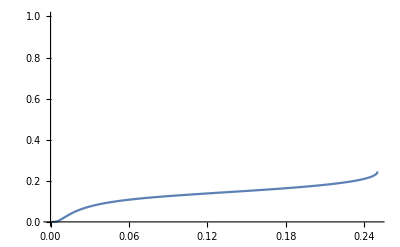

```mathematica
Plot[varFuncX[λ, 1.01]/sx^2, {λ, 0.001, 0.25}, PlotRange->{0, 1}]
```

```mathematica
ArrayPlot[meanArrayUncorrectedX, ColorFunction->(Blend[{{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->""],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, x0}]
Grid[N[Reverse[meanArrayUncorrectedX],8]]
```

-Graphics-

0.723607 | 0.723607 | 0.723607 | 0.723607 | 0.723607 | 0.723607 | 0.723607 | 0.723607
0.887298 | 0.887298 | 0.887298 | 0.887298 | 0.887298 | 0.887298 | 0.887298 | 0.887298
0.947214 | 0.947214 | 0.947214 | 0.947214 | 0.947214 | 0.947214 | 0.947214 | 0.947214
0.979583 | 0.979583 | 0.979583 | 0.979583 | 0.979583 | 0.979583 | 0.979583 | 0.979583
0.989898 | 0.989898 | 0.989898 | 0.989898 | 0.989898 | 0.989898 | 0.989898 | 0.989898
0.994975 | 0.994975 | 0.994975 | 0.994975 | 0.994975 | 0.994975 | 0.994975 | 0.994975
0.997996 | 0.997996 | 0.997996 | 0.997996 | 0.997996 | 0.997996 | 0.997996 | 0.997996
0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999

```mathematica
ArrayPlot[meanArrayX/.sx->0.1, ColorFunction->(Blend[{{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->""],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, x0}]
Grid[N[Reverse[meanArrayX/.sx->0.1],8]]
```

-Graphics-

0.716302 | 0.716402 | 0.716719 | 0.717275 | 0.718359 | 0.720706 | 0.722413 | 0.7233
0.868315 | 0.869111 | 0.871654 | 0.875645 | 0.881197 | 0.886361 | 0.887224 | 0.887296
0.907785 | 0.911941 | 0.923691 | 0.936346 | 0.944984 | 0.94718 | 0.947213 | 0.947214
0.89431 | 0.92087 | 0.96353 | 0.977881 | 0.979559 | 0.979583 | 0.979583 | 0.979583
0.872649 | 0.941171 | 0.986983 | 0.989869 | 0.989898 | 0.989898 | 0.989898 | 0.989898
0.898938 | 0.980817 | 0.99493 | 0.994975 | 0.994975 | 0.994975 | 0.994975 | 0.994975
0.98521 | 0.997902 | 0.997996 | 0.997996 | 0.997996 | 0.997996 | 0.997996 | 0.997996
0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999 | 0.998999